Rabi model with a classical drive to the atom
Can modify easily for studying a classical drive to the cavity
Motivation: How external drive modifies multiphoton resonance?

Module 1: Basic setting
Basis arrangement: (|e,0> |g,0> |e,1> |g,1> ... )
Ket: |α,n>, Position: (2n+2-α)

```mathematica
Clear["Global`*"];
nphoton=8; (* Max photon number *)
dim=2*(nphoton+1); (* Dimension of Hilbert space for one cavity *)

(* Parameters for the cavity *)
λ=0.05;
ωa=1;
ωc=1/3+3(λ/ωa)^2; (* frequency for 3-ph resonance *)
Ωeff=9Sqrt[6]λ^3/(4ωa^2); (* effective coupling for 3-photon resonance *)

(* Parameters for the external drive *)
ωp=0.1;
Ω=0.5Ωeff;
Tpp=π/Ω;

σz={{1,0},{0,-1}}; (* Pauli z for atom *)
σx={{0,1},{1,0}}; (* Pauli x for atom *)
σp={{0,1},{0,0}}; (* Raising for atom *)
σm={{0,0},{1,0}}; (* Lowering for atom *)

idenphoton=IdentityMatrix[nphoton+1];
idenatom=IdentityMatrix[2];

(* Annihilation for photon *)
a=Table[0.,nphoton+1,nphoton+1]; 
Do[a[[i,i+1]]=N[Sqrt[i]];,{i,1,nphoton}];

(* Creation for photon *)
adag=Transpose[a];

(* Rabi Hamiltonian for single cavity and a classical drive *)
H[t_]=ωa/2*KroneckerProduct[idenphoton,σz]+ωc*KroneckerProduct[adag.a,idenatom]+λ*KroneckerProduct[a+adag,σx]+Ω*Cos[ωp*t]*KroneckerProduct[idenphoton,σx];

(* Drop all counter-rotating effect *)
HJC[t_]=ωa/2*KroneckerProduct[idenphoton,σz]+ωc*KroneckerProduct[adag.a,idenatom]+λ*KroneckerProduct[a,σp]+λ*KroneckerProduct[adag,σm]+(Ω/2)*Exp[-ⅈ*ωp*t]*KroneckerProduct[idenphoton,σm]+(Ω/2)*Exp[ⅈ*ωp*t]*KroneckerProduct[idenphoton,σp];

(* Only drop counter-rotating effect for cavity coupling *)
HpJC[t_]=ωa/2*KroneckerProduct[idenphoton,σz]+ωc*KroneckerProduct[adag.a,idenatom]+λ*KroneckerProduct[a,σp]+λ*KroneckerProduct[adag,σm]+Ω*Cos[ωp*t]*KroneckerProduct[idenphoton,σx];
```

Module 2 : Numerical solving Schrodinger equation
Initial state: |g 0>

```mathematica
pos[α_,n_]:=(2n+2-α);
time=50*Tpp; 
interval=1000;

(* Time-dependent Schrodinger equation *)
functionlist=Table[Ψ[k][t],{k,1,dim}];
namelist=Table[Ψ[k],{k,1,dim}];
eqns=Thread[ⅈ*D[functionlist,t]==H[t].functionlist];

(* Initial quantum state *)
initial=Table[0,{k,1,dim}];
initial[[pos[0,0]]]=1;
Ψ0=Thread[functionlist==initial]/.t->0;
Clear[initial];

Timing[
sol=NDSolveValue[Join[eqns,Ψ0],namelist,{t,0,time},AccuracyGoal->10,PrecisionGoal->10];
wavfn=Table[Table[sol[[i]][t],{i,1,dim}]//Chop,{t,0,time,time/interval}]; 

nlist=Table[{(time/interval)*(i-1)/Tpp,Conjugate[wavfn[[i]]].KroneckerProduct[adag.a,idenatom].wavfn[[i]]//Chop},{i,1,interval+1}];
]
```

{36.7575,Null}

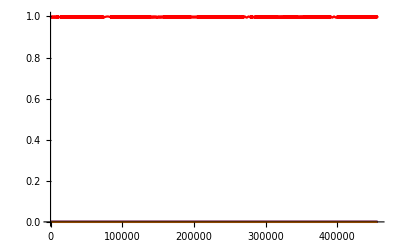

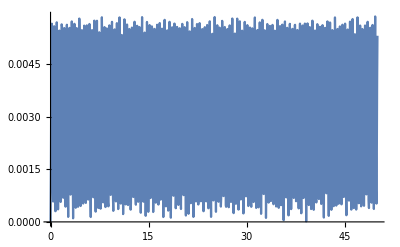

1.00002

```mathematica
Plot[{Evaluate[Abs[sol[[pos[0,0]]][t]]^2],Abs[sol[[pos[0,3]]][t]]^2,Abs[sol[[pos[0,1]]][t]]^2,Abs[sol[[pos[1,0]]][t]]^2,Abs[sol[[pos[1,4]]][t]]^2},{t,0,time},PlotStyle->{Red,Black,Blue,Purple,Orange},AxesOrigin->{0,0},PlotRange->Full]

ListPlot[nlist,AxesOrigin->{0,0},Joined->True,PlotRange->Full]
Evaluate[Sum[Abs[sol[[i]][time]]^2,{i,1,dim}]]
```